## Зададим необходимые функции

```mathematica
ClearAll[F,r2,φ,X,Y];
```

```mathematica
F[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2[n_,r1_,F_] := 1/(F(n-1))+r1;
φ[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
X[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Y[F_,φout_,y_]:=2F Tan[-φout]-y;
```

## Построим график зависимости продольной аберрации от величины обратной к радиусу одной из сферической поверхности, образующих линзу r1=1/R1

Варьируется фокусное расстояние линзы F0, поперечный размер линзы H и показатель преломления стекла n. Внизу графика выводится положение минимума и значение r2, которые рассчитывается по значению F0 и r2

```mathematica
Manipulate[
Grid[
{
{
Plot[
X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2],
{r1,-0.1,0.1},PlotRange->{{-0.1,0.1},{0,10}},GridLines->{Range[-0.1,0.1,0.01], Range[0,20,0.5]},
Ticks->{Range[-0.1,0.1,0.02],Range[0,10,1]},
ImageSize->400
]
},
{
min=FindMinimum[
X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
,{r1,-0.1,0.1}]
},
{
"r_2= "<>ToString[r2[n,r1/.min⟦2⟧,F0]]
}
}
],
{{F0,40,"F_0"},20,300},
{{H,10,"H"},1,20},
{{n,1.5,"n"},1.001,3}
]
```

FindMinimum::nrnum: The function value 123.+4.74 Cot[ArcSin[4.74 r2[1.986,-0.1,61.5]]-ArcSin[1.986 Sin[«1»]]] is not a real number at {r1} = {-0.1}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-0.001,-0.1,0.1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Мы задаем r1, r2 F - как функция; строим график X(H/4F)

По заданному фокусному расстоянию мы можем рассчитать такие значения r1 и r2, которые нам делают минимальную продольную аберрацию. (внизу графика)

Исходя из изменения параметров можно сделать выводы
1. При увеличении фокусного расстояния F0 (при этом H0 фиксировано, то есть отношение F0/H увеличивается) минимальная продольная аберрация уменьшается
2. При увеличении размера линзы H (F0 фиксировано, отношение F0/H уменьшается) продольная аберрация увеличивается
3. При стремлении показателя преломления к бесконечности минимальная продольная аберрация стремится к нулю.

## Проверим правило 4П

Сначала помещаем линзу так, чтобы свет падал сначала на плоскую поверхность, а потом на сферическую . Затем наоборот

```mathematica
Manipulate[
Grid[
{
{
(* Продольная аберрация, если первая поверхность плоская *)
XP1=X[F0,φ[n,r2[n,0,F0],φ[1/n,0,ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_(1  x)(0)= "<>ToString[XP1]
},
{(* Поперечная аберрация, если первая поверхность плоская *)
YP1 = Y[F0,φ[n,r2[n,0,F0],φ[1/n,0,ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_(1  y)(0)= "<>ToString[YP1]
},
{
XP2=X[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_(2  x)(0)= "<>ToString[XP2]
},
{
YP2=Y[F0,φ[n,r2[n,1/(F0(1-n)),F0],φ[1/n,1/(F0(1-n)),ArcTan[H/(4 F0)],H/2],H/2],H/2];
"(:041f)_(2  y)(0)= "<>ToString[YP2]
}(*,
{
(*r2[n,1/(F0(1-n)),F0]*)
}*)
}
],

{{F0,40,"F_0"},0,100},
{{H,10,"H"},1,20},
{{n,1.5,"n"},1.001,3}
]
```

Можно видеть, что в первом случае  и продольная, и поперечная аберрации больше чем во втором. Следовательно, правило 4П работает. Ниже представлен слайд с лекции по общей физики на эту тему .

```mathematica
-Graphics-;
```

## Распределение интенсивности внутри кружка-изображения

Построим распределение интенсивности внутри кружка-изображения.

### Зададим необходимые функции

```mathematica
Yk[k_]:=Y[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
Xk[k_]:=X[F0,φ[n,r2[n,r1,F0],φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)],(H*k)/(2*K)],(H*k)/(2*K)];
Ik[k_]:=I0*1/(K^2+((H k)/(4F))^2)*(2k+1)/(Yk[k]-Yk[k-1]);
```

Yk обозначает радиус кружка-изображения, Xk - величина продольной аберрации, Ik - интенсивность кружочка.00, Сб ввлдоа

```mathematica
ClearAll[data,colornorm,color,disks,colordisks]
```

```mathematica
K=100;I0 = 1;  H=10;F=40;r1=-0.001;n=1.5;F0=40;
```

```mathematica
data =Ik/@Range[1,K];
colornorm = 1/(Max[data]-Min[data])*(data-Min[data]);
color = Hue[0.1,#,1]&/@ colornorm;
disks =Disk[{0,0},#]&/@Map[Yk,Range[1,K]];
colordisks=Reverse[Table[List[color⟦i⟧,disks⟦i⟧],{i,1,K}]];
Manipulate[
Grid[{{
Graphics[colordisks⟦-n;;⟧,ImageSize->400],
Plot[Ik[k],{k,1,K},AxesLabel->{"K","I"},PlotRange->{{0,100},{0,1000}},ImageSize->400],
Plot[Yk[k],{k,1,K},AxesLabel->{"K","R"},PlotRange->{{0,100},{0,Yk[K]}},ImageSize->400]
}}],
{n,1,K,1}
]
```

Из анимации и графиков хорошо видно, что при отдалении от центрального кружка интенсивность последующих кружков резко падает, при этом их радиус достаточно быстро растет.

### Плоскость наиболее отчетливого изображения

Убирая из рассмотрения крайние зоны (их интенсивность в разы меньше) находим такое K (количество оставленных зон), что радиус Yk[K] равен размеру дифракционного пятна.  Плоскость где радиус пятна равен отношению λ/H будем считать плоскостью наиболее отчетливого изображения

```mathematica
λ=600*10^-9; H=0.1;
λ/H
```

6.×10^-6

```mathematica
I0 = 1; K=10; H=10;F=40;r1=-0.001;
```

```mathematica
Map[Yk,Range[1,10]]
```

{0.000328925,0.00263635,0.00892571,0.0212511,0.0417446,0.0726461,0.116337,0.175378,0.252556,0.350936}

```mathematica
(Xk[1]-Xk[K])*Tan[φ[1/n,r1,ArcTan[(H*1)/(4 F0*K)],(H*1)/(2*K)]]
```

-0.0207762

```mathematica
FindMinimum[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,100}]
```

{-0.272034,{k→8.65425}}

```mathematica
Min[Table[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,K}]]
```

-0.271376

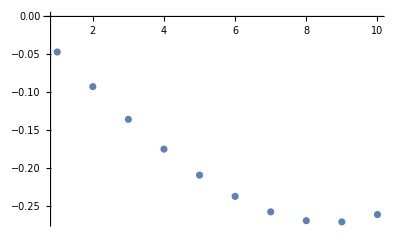

```mathematica
ListPlot[Table[(Xk[k]-Xk[15])*Tan[φ[1/n,r1,ArcTan[(H*k)/(4 F0*K)],(H*k)/(2*K)]],{k,1,K}],PlotRange->All]
```

## Пункт 2)

Помещаем вплотную к первой линзе вторую линзу такого же диаметра. Подберем параметры линз таким образом, чтобы минимизировать сферическую аберрацию (по сравнению с одной линзой с таким же фокусным расстоянием F для параксиальных лучей).

### Зададим необходимые функции для данного случая

```mathematica
ClearAll[F,R2,φ,X,Y,PX,r1,r2]
```

F - фокусное расстояние системы

```mathematica
F[n_,r1_,r2_]:=1/((n-1)(r2-r1));
R2[n_,r1_,F_] := 1/(F(n-1))+r1;
φ[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
X[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Y[F_,φout_,y_]:=2F Tan[-φout]-y;
```

```mathematica
PX[r1_,r2_,ρ1_,n1_,n2_,F0_,H_] := X[F0,
φ[
n2,
R2[n2,ρ1,(F[n1,r1,r2] F0)/(F[n1,r1,r2]-F0)],
φ[
1/n2,
ρ1,
φ[
n1,
r2,
φ[1/n1,
r1,
ArcTan[H/(4F0)],
H/2],
H/2],
H/2],
H/2],
H/2];
```

```mathematica
ClearAll[ρ1,n1,n2]
F0=40;H=10;n1=1.5;n2=2;
```

```mathematica
min=FindMinimum[
{PX[r1,r2,ρ1,n1,n2,F0,H],
-0.1≤r1≤0.1,
-0.1≤r2≤0.1,
-0.1≤ρ1≤0.1,
1.1≤n1≤4,
1.1≤n2≤4,
r1<r2},
{r1,-0.01},
{r2,0},
{ρ1,-0.01},
{n1,1.5},
{n2,1.5}
]
```

{0.312174,{r1→0.0013769,r2→0.00554359,ρ1→-0.00557067,1.5→3.99999,2→3.99999}}

Уже есть какая-то линза и мы подбираем вторую

```mathematica
min=FindMinimum[
{PX[r1,r2,ρ1,n1,n2,F0,H],
-0.02≤r1≤-0.02,
0.01≤r2≤0.01,
-0.1≤ρ1≤0.1,
1.1≤n1≤2,
1.1≤n2≤2,
r1<r2},
{r1,-0.02},
{r2,0.01},
{ρ1,-0.01},
{n1,1.5},
{n2,1.5}
]
```

{0.859168,{r1→-0.02,r2→0.01,ρ1→-0.0110326,1.5→1.2539,2→2.}}

Поиск ρ2

```mathematica
R2[n2,ρ1/.min⟦2,3⟧,(F[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧] F0)/(F[n1,r1/.min⟦2,1⟧,r2/.min⟦2,2⟧]-F0)]
```

-0.00103262

```mathematica
Manipulate[
Plot[PX[r1,r2,ρ1,n1,n2,F0,H],{ρ1,-0.1,0.1},PlotRange->All],
{{r1,-0.004,"r1"},-0.1,0.1},
{{r2,0.014,"r2"},-0.1,0.1}
]
```

Power::infy: Infinite expression 1/0. encountered.